# p_n-PPT criteria for continuous-variable systems

Serge Deside, Tobias Haas and Nicolas J. Cerf

Centre for Quantum Information and Communication, École polytechnique de Bruxelles, CP 165, Université libre de Bruxelles, 1050 Brussels, Belgium

We evaluate the p_n-PPT criteria for various states.

Information and Instructions

The notebook is auto-run

Edit ‘Definitions and Options’ if necessary, then run the whole notebook

```mathematica
(* Evaluate here to run the notebook. *)
```

Definitions and Options

### Precision

```mathematica
(* Set precision used for plots. Higher precision (approx. 100) needed for high-quality figures, but this comes at the expense of computing time. *)
InternalPlotPoints=100;
```

### Saving/Loading

```mathematica
(* Set directory. *)
SetDirectory[NotebookDirectory[]];
```

### Global assumptions

```mathematica
(* Set global assumptions. *)
$Assumptions={Element[n,Integers],n>0,α>0,β>0,0<z<1,σm>0,σp>0,Element[n1,Integers],n1≥0,Element[n2,Integers],n2≥0};
```

### Plotting

```mathematica
(* Define standard colors for figures. *)
PlotColors={RGBColor[0.206756,0.371758,0.553117,1.],RGBColor[0.120565,0.596422,0.543611,1.],RGBColor[0.404001,0.800275,0.362552,1.],RGBColor[0.8784313725490196,0.403921568627451,0.4549019607843137,1],RGBColor[101/128,5/8,113/256]};

(* The same with opacity. *)
PlotColorsOpacity={RGBColor[0.206756,0.371758,0.553117,0.1],RGBColor[0.120565,0.596422,0.543611,0.2],RGBColor[0.404001,0.800275,0.362552,0.3],RGBColor[0.8784313725490196,0.403921568627451,0.4549019607843137,0.4]};

(* Define continuous colors. *)
ContinuousColors=ColorData[{"BlueGreenYellow",{5,1}}];

(* Define nice plotmarkers for ListPlot[...]. *)
NicePlotmarkers[size_,edgethickness_,backgroundcolor_,edgecolor_,form_]:={Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Thickness[edgethickness]]],Disk[{0,0},1]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Thickness[edgethickness]]],Triangle[{{0,0},{1,0},{1/2,Sqrt[3]/2}}]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Thickness[edgethickness]]],Polygon[{{0,0},{1/2,-1/2},{1,0},{1/2,1/2}}]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Thickness[edgethickness]]],Rectangle[{-1/2,-1/2},{1/2,1/2}]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Thickness[edgethickness]]],Triangle[{{0,0},{1,0},{1/2,-Sqrt[3]/2}}]},ImageSize->size]}[[form]];
```

Gaussian states

### Moments & criteria

#### p_n-moments

```mathematica
(* Set up the k-th. moment in terms of symplectic eigenvalues. *)
pnGaussian[ν1_,ν2_,k_]:=((2^k)/(((ν1+1)^k)-(ν1-1)^k))*((2^k)/(((ν2+1)^k)-(ν2-1)^k))//Simplify;
```

#### p_n-PPT criterion

```mathematica
(* Set up the general criterion as the moment matrix. Check for semi-positivity by using 'PositiveSemidefiniteMatrixQ'. When this evaluates to 'False', entanglement is detected. *)
pnPPTGaussian[ν1_,ν2_,k_]:=Table[pnGaussian[ν1,ν2,i+j+1],{i,0,(k-1)/2,1},{j,0,(k-1)/2,1}];
```

#### p_3-PPT criterion

```mathematica
(* Set up the p3-PPT criterion as a difference between LHS and RHS of the corresponding inequality. *)
p3PPTGaussian[ν1_,ν2_]:=pnGaussian[ν1,ν2,3]-pnGaussian[ν1,ν2,2]^2;
```

#### Neven p_3-PPT criterion

```mathematica
(* Now, set up the Neven criterion of order 3 in the same fashion. *)
Nevenp3PPTGaussian[ν1_,ν2_]=pnGaussian[ν1,ν2,3]+(1/2)-(3/2)*pnGaussian[ν1,ν2,2]//Simplify;
```

#### Optimal p_3-PPT criterion

```mathematica
(* Set up helper functions first. *)

(* Floor of 1/Subscript[p, 2]. *)
αGaussian[ν1_,ν2_]:=Floor[1/pnGaussian[ν1,ν2,2]];

(* x function. *)
xGaussian[ν1_,ν2_]:=(αGaussian[ν1,ν2]+Sqrt[αGaussian[ν1,ν2]*(pnGaussian[ν1,ν2,2]*(αGaussian[ν1,ν2]+1)-1)])/(αGaussian[ν1,ν2]*(αGaussian[ν1,ν2]+1));
```

```mathematica
(* At last, we set up the optimal criterion of order 3. *)
Op3PPTGaussian[ν1_,ν2_]=pnGaussian[ν1,ν2,3]-αGaussian[ν1,ν2]*(xGaussian[ν1,ν2]^3)-(1-αGaussian[ν1,ν2]*xGaussian[ν1,ν2])^3//Simplify;
```

```mathematica
(* The same as function of p2 (with a little trick for visualization purposes). *)
Op3PPTGaussian2[p2_]:=If[p2≤1,Module[{xInternal=(Floor[1/p2]+Sqrt[Floor[1/p2]*(p2*(Floor[1/p2]+1)-1)])/(Floor[1/p2]*(Floor[1/p2]+1))},Floor[1/p2]*xInternal^3+(1-Floor[1/p2]*xInternal)^3],2];
```

#### Simon in terms of moments

```mathematica
(* We also rewrite Simon's criterion in terms of Subscript[p, 2] and Subscript[p, 3]. To that end, we solve for the symplectic eigenvalues first. *)
νSolved=Solve[pnGaussian[ν1,ν2,2]==p2&&pnGaussian[ν1,ν2,3]==p3,{ν1,ν2}][[4]]//FullSimplify
```

{ν1→(√((-p2^2 (-16+p3)-9 p3+√(-36 p2^2 p3^2+(p2^2 (-16+p3)+9 p3)^2))/(p2^2 p3)))/(√6),ν2→(√6)/(p2 √((-p2^2 (-16+p3)-9 p3+√(-36 p2^2 p3^2+(p2^2 (-16+p3)+9 p3)^2))/(p2^2 p3)))}

```mathematica
(* Set the results as definitions *)
ν1Solved[p2_,p3_]=ν1/.νSolved[[1]];
ν2Solved[p2_,p3_]=ν2/.νSolved[[2]];
```

```mathematica
(* For consistency, we check that their inverse product is the purity. *)
1/(ν1Solved[p2,p3]*ν2Solved[p2,p3])//Simplify
```

p2

```mathematica
(* Now, we solve for the point where both symplectic eigenvalues are 1. *)
Superp2=Solve[ν1Solved[p2,p3]==1,p3][[1]]
Superp3=Solve[ν2Solved[p2,p3]==1,p3][[1]]
```

{p3→(4 p2^2)/(3+p2^2)}

{p3→(4 p2^2)/(3+p2^2)}

```mathematica
(* At last, we set the result as another criterion. *)
SimonCriterionMoments[p2_,p3_]=p3-(p3/.Superp2);

(* The same in terms of the symplectic eigenvalues. *)
SimonCriterionSymplectic[ν1_,ν2_]=SimonCriterionMoments[pnGaussian[ν1,ν2,2],pnGaussian[ν1,ν2,3]]//FullSimplify;
```

```mathematica
(* Find upper bound on p3 by physicality. *)
(Maximize[pnGaussian[ν1,1/(ν1*p2),3],ν1]//Simplify)[[1]]
```

Piecewise[{{(16 p2^2)/(-3+p2)^2, p2≤0}, {(16 p2^2)/(3+p2)^2, True}}]

#### Relations

```mathematica
(* Find intersection between Neven and p3-PPT. *)
p3PPTNevenIntersection1=Module[{SolutionInternal=NSolve[Nevenp3PPTGaussian[ν1,ν2]==p3PPTGaussian[ν1,ν2]&&Nevenp3PPTGaussian[ν1,ν2]==0&&p3PPTGaussian[ν1,ν2]==0&&ν1>1,{ν1,ν2},Reals][[1]]},{ν1/.SolutionInternal,ν2/.SolutionInternal}];
p3PPTNevenIntersection2=Module[{SolutionInternal=NSolve[Nevenp3PPTGaussian[ν1,ν2]==p3PPTGaussian[ν1,ν2]&&Nevenp3PPTGaussian[ν1,ν2]==0&&p3PPTGaussian[ν1,ν2]==0&&ν1>1,{ν1,ν2},Reals][[1]]},{ν2/.SolutionInternal,ν1/.SolutionInternal}];
```

```mathematica
(* Check purity at this point, should be 1/2. *)
1/(2.9208096264818906*0.6847416489820993)
```

0.5

### TMSV state at finite temperature

```mathematica
(* We set up the symplectic eigenvalues of the two-mode squeezed vacuum (TMSV) state as functions of ϵ and λ. *)
TSMVFiniteTemperature1[ϵ_,r_]:={Exp[-2*r]*(1+ϵ)/(1-ϵ),Exp[2*r]*(1+ϵ)/(1-ϵ)};
TSMVFiniteTemperature2[ϵ_,r_]:={Exp[2*r]*(1+ϵ)/(1-ϵ),Exp[-2*r]*(1+ϵ)/(1-ϵ)};
```

```mathematica
(* We determine the required ϵ for the state's purity to equal 1/2. *)
TMSVFiniteTemperatureϵ=(ϵ/.Solve[pnGaussian[Exp[-2*r]*(1+ϵ)/(1-ϵ),Exp[2*r]*(1+ϵ)/(1-ϵ),2]==1/2,ϵ∈Interval[{0,1}]][[1]])[[1]]
```

3-2 √2

```mathematica
(* Thereupon, we compute the intersections with the higher-order pn-PPT criteria. *)
TMSVFiniteTemperaturerp3=Module[{EigenvaluesInternal=Eigenvalues[pnPPTGaussian[TSMVFiniteTemperature1[TMSVFiniteTemperatureϵ,r][[1]],TSMVFiniteTemperature1[TMSVFiniteTemperatureϵ,r][[2]],3]]//Simplify},r/.FindRoot[EigenvaluesInternal[[1]],{r,0.3}][[1]]]
TMSVFiniteTemperaturerp5=Module[{EigenvaluesInternal=Eigenvalues[pnPPTGaussian[TSMVFiniteTemperature1[TMSVFiniteTemperatureϵ,r][[1]],TSMVFiniteTemperature1[TMSVFiniteTemperatureϵ,r][[2]],5]]//Simplify},r/.FindRoot[EigenvaluesInternal[[1]],{r,0.2}][[1]]]
TMSVFiniteTemperaturerp7=Module[{EigenvaluesInternal=Eigenvalues[pnPPTGaussian[TSMVFiniteTemperature1[TMSVFiniteTemperatureϵ,r][[1]],TSMVFiniteTemperature1[TMSVFiniteTemperatureϵ,r][[2]],7]]//Simplify},r/.NSolve[EigenvaluesInternal[[1]]==0,r,PositiveReals][[1]]]
```

0.362644

0.220838

0.187117

### Plots

#### Third-order criteria in (ν1,ν2) plane

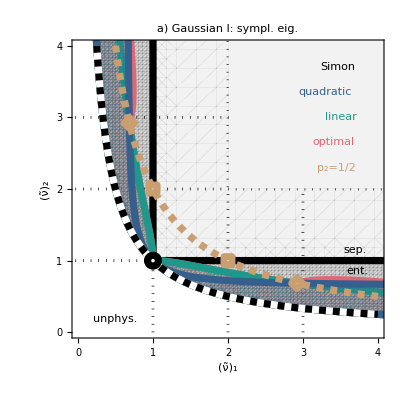

```mathematica
(* We show the regions where the different criteria of third order witness entanglement together with Simon's criterion. *)
p3GaussianPlot=Quiet[Show[RegionPlot[{ν1≥1&&ν2≥1},{ν1,0,5},{ν2,0,5},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->{{Gray,Opacity[0.1]}},BoundaryStyle->{{Black,Thickness[0.013]}},PlotRange->{{0,4},{0,4}},FrameLabel->{Style["(ν̃)_1",Black,FontSize->15],Style["(ν̃)_2",Black,FontSize->15]},FrameTicks->{{{0,1,2,3,4},None},{{0,1,2,3,4},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{1,2,3},{1,2,3}},GridLinesStyle->Directive[Black,Thickness[0.005],Dotted],PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["a) ",Black,FontSize->16,Bold],Style["Gaussian I: sympl. eig.",Black,FontSize->15]}],Alignment->Center,ImageSize->{170,Automatic}]],RegionPlot[(ν1≤1||ν2≤1)&&ν1*ν2≥1,{ν1,0,5},{ν2,0,5},PlotStyle->{Gray,Opacity[0.3]},BoundaryStyle->Directive[Thickness[0.01],Black],PlotPoints->InternalPlotPoints],
RegionPlot[{Op3PPTGaussian[ν1,ν2]≤0&&ν1*ν2≥1},{ν1,0,5},{ν2,0,5},PlotStyle->{PlotColorsOpacity[[4]]},BoundaryStyle->Directive[Thickness[0.013],PlotColors[[4]]],PlotPoints->InternalPlotPoints],
RegionPlot[{Nevenp3PPTGaussian[ν1,ν2]≤0&&ν1*ν2≥1},{ν1,0,5},{ν2,0,5},PlotStyle->{PlotColorsOpacity[[2]]},BoundaryStyle->Directive[Thickness[0.013],PlotColors[[2]]],PlotPoints->InternalPlotPoints],
RegionPlot[p3PPTGaussian[ν1,ν2]≤0&&ν1*ν2≥1,{ν1,0,5},{ν2,0,5},PlotStyle->{PlotColorsOpacity[[1]]},BoundaryStyle->Directive[Thickness[0.013],PlotColors[[1]]],PlotPoints->InternalPlotPoints],Plot[{1/ν1,2/ν1,1/ν1},{ν1,0.2,4},PlotRange->{0,4},PlotStyle->{{Thickness[0.013],White},{Thickness[0.013],PlotColors[[5]],Dashed},{Thickness[0.013],Black,Dashed}}],
ListPlot[{{{1,1}},{p3PPTNevenIntersection1,p3PPTNevenIntersection2},{{2,1},{1,2}}},PlotMarkers->{NicePlotmarkers[11,0.28,White,Black,1],NicePlotmarkers[11,0.25,White,PlotColors[[5]],3],NicePlotmarkers[8.25,0.3375,White,PlotColors[[5]],4]}],Graphics[{White,Rectangle[{2.01,2.01},{5,5}],Opacity[0.1],Gray,Rectangle[{2.001,2.001},{5,5}],Opacity[1],FontSize->13,Black,Text["Simon",{3.46,3.7}],PlotColors[[1]],Text["quadratic",{3.295,3.35}],PlotColors[[2]],Text["linear",{3.505,3}],PlotColors[[4]],Text["optimal",{3.41,2.65}],PlotColors[[5]],Text["p_2=1/2",{3.44,2.3}],FontSize->11,Black,Text["unphys.",{0.5,0.19}],Text["sep.",{3.7,1.155}],Text["ent.",{3.72,0.85}]}],ImageSize->{Automatic,250},AspectRatio->1]]
```

#### Third-order criteria in (p2,p3) plane

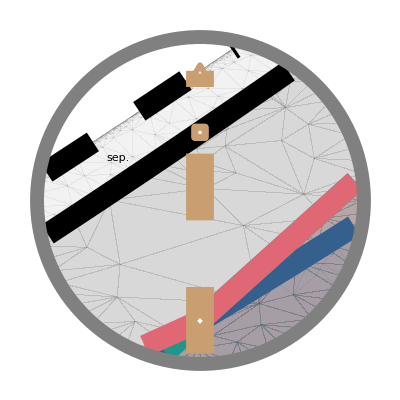

```mathematica
(* First, we plot the inset. *)
p3GaussianPlot2Inset=Show[Graphics[{White,Disk[{0.5,0.287},{0.03,0.05}]}],RegionPlot[{SimonCriterionMoments[p2,p3]<0},{p2,p3}∈Disk[{0.5,0.287},{0.03,0.05}],PlotTheme->"Detailed",PlotLegends->None,PlotStyle->{{Gray,Opacity[0.3]}},BoundaryStyle->None,PlotPoints->InternalPlotPoints,Frame->None,GridLines->None],RegionPlot[True,{p2,p3}∈RegionIntersection[Disk[{0.5,0.287},{0.03,0.05}],ImplicitRegion[(4*p2^2)/(3+p2^2)≤p3≤(16 p2^2)/(3+p2)^2,{p2,p3}]],PlotStyle->{{Gray,Opacity[0.1]}},BoundaryStyle->None],RegionPlot[Op3PPTGaussian2[p2]>p3,{p2,p3}∈Disk[{0.5,0.287},{0.03,0.05}],PlotStyle->{PlotColorsOpacity[[4]]},BoundaryStyle->None],RegionPlot[(3/2)*p2-1/2>p3,{p2,p3}∈Disk[{0.5,0.287},{0.03,0.05}],PlotStyle->{PlotColorsOpacity[[2]]},BoundaryStyle->None],RegionPlot[p2^2>p3,{p2,p3}∈Disk[{0.5,0.287},{0.03,0.05}],PlotStyle->{PlotColorsOpacity[[1]]},BoundaryStyle->None],
Plot[{(16 p2^2)/(3+p2)^2,(4*p2^2)/(3+p2^2),p2^2,(3/2)*p2-1/2,Op3PPTGaussian2[p2]},{p2,0.45,0.55},PlotStyle->{{Black,Thickness[0.04],Dashing[0.1]},{Black,Thickness[0.04]},{PlotColors[[1]],Thickness[0.04]},{PlotColors[[2]],Thickness[0.04]},{PlotColors[[4]],Thickness[0.04]}},RegionFunction->Function[{p2,p3},0<Sqrt[(p2-0.5)^2/0.03^2+(p3-0.287)^2/0.05^2]<0.955]],Graphics[{FontSize->10,Text["sep.",{0.485,0.3},Automatic,{0.78,0.5}],PlotColors[[5]],Thickness[0.05],Dashing[0.12],Line[{{1/2,0.24},{1/2,16/49}}],Dashing[None],Gray,Thickness[0.025],Circle[{0.5,0.287},{0.03,0.05}]}],ListPlot[{{{1/2,1/4}},{{1/2,4/13}},{{1/2,16/49}}},PlotMarkers->{NicePlotmarkers[14,0.2,White,PlotColors[[5]],3],NicePlotmarkers[10.5,0.27,White,PlotColors[[5]],4],NicePlotmarkers[13,0.2,White,PlotColors[[5]],2]}],AspectRatio->1,ImageSize->{Automatic,70}]
```

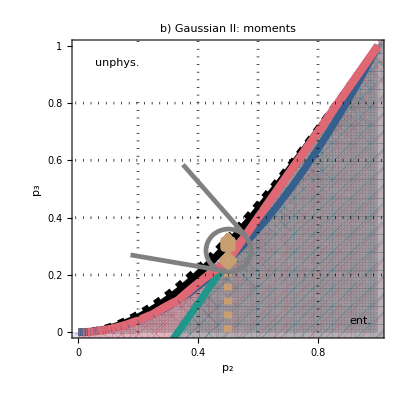

```mathematica
(* Then, we plot the four criteria at third order as functions of the partial moments. *)
p3GaussianPlot2=Show[RegionPlot[{SimonCriterionMoments[p2,p3]<0,(4*p2^2)/(3+p2^2)≤p3≤(16 p2^2)/(3+p2)^2},{p2,0,1},{p3,0,1},PlotTheme->"Detailed",PlotRange->{{0,1},{0,1}},PlotLegends->None,PlotStyle->{{Gray,Opacity[0.3]},{Gray,Opacity[0.1]}},BoundaryStyle->None,PlotPoints->InternalPlotPoints,FrameLabel->{Style["p_2",Black,FontSize->15],Style["p_3",Black,FontSize->15]},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},None},{{0,0.2,0.4,0.6,0.8,1},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0.2,0.4,0.6,0.8},{0.2,0.4,0.6,0.8}},GridLinesStyle->Directive[Black,Thickness[0.005],Dotted],PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["b) ",Black,FontSize->16,Bold],Style["Gaussian II: moments",Black,FontSize->15]}],Alignment->Center,ImageSize->170],Epilog->Inset[p3GaussianPlot2Inset,{0.22,0.45}]],RegionPlot[Op3PPTGaussian2[p2]>p3,{p2,0,1.1},{p3,-0.1,1.1},PlotStyle->{PlotColorsOpacity[[4]]},BoundaryStyle->None],RegionPlot[(3/2)*p2-1/2>p3,{p2,-0.1,1.1},{p3,-0.1,1.1},PlotStyle->{PlotColorsOpacity[[2]]},BoundaryStyle->None],RegionPlot[p2^2>p3,{p2,-0.1,1.1},{p3,-0.1,1.1},PlotStyle->{PlotColorsOpacity[[1]]},BoundaryStyle->None],
Plot[{(16 p2^2)/(3+p2)^2,(4*p2^2)/(3+p2^2),p2^2,(3/2)*p2-1/2,Op3PPTGaussian2[p2]},{p2,0,1},PlotStyle->{{Black,Thickness[0.013],Dashed},{Black,Thickness[0.013]},{PlotColors[[1]],Thickness[0.013]},{PlotColors[[2]],Thickness[0.013]},{PlotColors[[4]],Thickness[0.015]}}],Graphics[{White,Rectangle[{0,0.805},{0.395,1}],PlotColors[[5]],Thickness[0.015],Dashed,Line[{{1/2,0},{1/2,4/13}}],FontSize->11,Black,Text["unphys.",{0.13,0.94}],Text["ent.",{0.94,0.04}],Gray,Dashing[None],Thickness[0.0085],Circle[{0.5,0.287},0.075],Line[{{0.35,0.585},{0.56,0.335}}],Line[{{0.175,0.27},{0.5,0.287-0.075}}]}],ListPlot[{{{1/2,1/4}},{{1/2,4/13}},{{1/2,16/49}}},PlotMarkers->{NicePlotmarkers[11,0.25,White,PlotColors[[5]],3],NicePlotmarkers[8.25,0.3375,White,PlotColors[[5]],4],NicePlotmarkers[143/14,0.25,White,PlotColors[[5]],2]}],ImageSize->{Automatic,250},AspectRatio->1]
```

#### Higher-order criteria in (ν1,ν2) plane

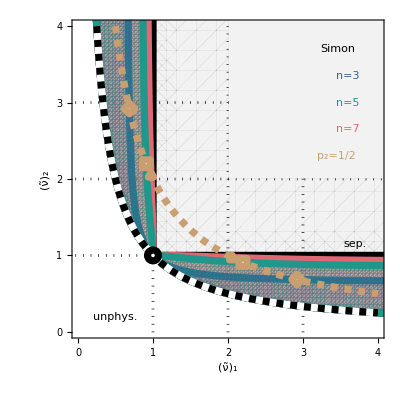

```mathematica
(* We show the regions where the higher-order criteria witness entanglement together with Simon's criterion. *)
p357GaussianPlot=Quiet[Show[RegionPlot[{ν1≥1&&ν2≥1},{ν1,0,5},{ν2,0,5},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->{{Gray,Opacity[0.1]}},BoundaryStyle->Opacity[0],PlotRange->{{0,4},{0,4}},GridLines->{{1,2,3},{1,2,3}},GridLinesStyle->Directive[Black,Thickness[0.005],Dotted],FrameLabel->{Style["(ν̃)_1",Black,FontSize->15],Style["(ν̃)_2",Black,FontSize->15]},FrameTicks->{{{0,1,2,3,4},None},{{0,1,2,3,4},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15]],RegionPlot[(ν1≤1||ν2≤1)&&ν1*ν2≥1,{ν1,0,5},{ν2,0,5},PlotStyle->{Gray,Opacity[0.35]},BoundaryStyle->Directive[Thickness[0.013],Black],PlotPoints->InternalPlotPoints],RegionPlot[Not[PositiveSemidefiniteMatrixQ[pnPPTGaussian[ν1,ν2,7]]]&&ν1*ν2≥1,{ν1,0,5},{ν2,0,5},PlotStyle->{PlotColorsOpacity[[4]]},BoundaryStyle->Directive[Thickness[0.013],PlotColors[[4]]],PlotPoints->InternalPlotPoints],
RegionPlot[{Not[PositiveSemidefiniteMatrixQ[pnPPTGaussian[ν1,ν2,3]]]&&ν1*ν2≥1},{ν1,0,5},{ν2,0,5},PlotStyle->{PlotColorsOpacity[[1]]},BoundaryStyle->Directive[Thickness[0.013],PlotColors[[1]]],PlotPoints->InternalPlotPoints],
RegionPlot[Not[PositiveSemidefiniteMatrixQ[pnPPTGaussian[ν1,ν2,5]]]&&ν1*ν2≥1,{ν1,0,5},{ν2,0,5},PlotStyle->{PlotColorsOpacity[[2]]},BoundaryStyle->Directive[Thickness[0.013],PlotColors[[2]]],PlotPoints->InternalPlotPoints],
Plot[{1/ν1,2/ν1,1/ν1},{ν1,0.2,4},PlotRange->{0,4},PlotStyle->{{Thickness[0.013],White},{Thickness[0.013],PlotColors[[5]],Dashed},{Thickness[0.013],Black,Dashed}}],
ListPlot[{{{1,1}},{TSMVFiniteTemperature1[TMSVFiniteTemperatureϵ,TMSVFiniteTemperaturerp3],TSMVFiniteTemperature2[TMSVFiniteTemperatureϵ,TMSVFiniteTemperaturerp3]},{TSMVFiniteTemperature1[TMSVFiniteTemperatureϵ,TMSVFiniteTemperaturerp5],TSMVFiniteTemperature2[TMSVFiniteTemperatureϵ,TMSVFiniteTemperaturerp5]},{TSMVFiniteTemperature1[TMSVFiniteTemperatureϵ,TMSVFiniteTemperaturerp7],TSMVFiniteTemperature2[TMSVFiniteTemperatureϵ,TMSVFiniteTemperaturerp7]}},PlotMarkers->{NicePlotmarkers[11,0.28,White,Black,1],NicePlotmarkers[11,0.25,White,PlotColors[[5]],3],NicePlotmarkers[8.25,0.3375,White,PlotColors[[5]],4],NicePlotmarkers[143/14,0.25,White,PlotColors[[5]],2]}],Graphics[{White,Rectangle[{2.01,2.01},{5,5}],Opacity[0.1],Gray,Rectangle[{2.001,2.001},{5,5}],Opacity[1],FontSize->13,Black,Text["Simon",{3.46,3.7}],PlotColors[[1]],Text["n=3",{3.6,3.35}],PlotColors[[2]],Text["n=5",{3.6,3}],PlotColors[[4]],Text["n=7",{3.6,2.65}],PlotColors[[5]],Text["p_2=1/2",{3.44,2.3}],FontSize->11,Black,Text["unphys.",{0.5,0.19}],Text["sep.",{3.7,1.155}]}],ImageSize->{Automatic,233}]]
```

#### Combined plot

```mathematica
(* We combine the latter three plots into a single graphic. *)
Grid[{{p3GaussianPlot,p3GaussianPlot2,p357GaussianPlot},{}},Spacings->{0.2,0},Alignment->Bottom]
```

-Graphics- | -Graphics- | -Graphics-
 |  |

Gaussian mixtures

### Schrödinger cat states

#### p_n-moments & criteria

```mathematica
(* Normalization constant. *)
CatNormalizationOdd[α_, β_,z_]= 1/(2*(1-(1-z)Exp[-2(Abs[α]^2+Abs[β]^2)]));

(* We set up the two lowest-order moments for the odd Schrödinger cat state. *)
p2CatOdd[α_, β_,z_]=2CatNormalizationOdd[α, β,z]^2 ((1+(1-z)^2)(1+Exp[-4(Abs[α]^2+Abs[β]^2)])-4(1-z)Exp[-2(Abs[α]^2+Abs[β]^2)])//FullSimplify;
p3CatOdd[α_, β_,z_]=2CatNormalizationOdd[α, β,z]^3(1+3*Exp[-4(Abs[α]^2+Abs[β]^2)]-3*(1-z)*Exp[-2(Abs[α]^2+Abs[β]^2)]*(2+Exp[-4Abs[α]^2]+Exp[-4Abs[β]^2])+3*((1-z)^2)*Exp[-4(Abs[α]^2+Abs[β]^2)]*(2+Exp[4Abs[α]^2]+Exp[4Abs[β]^2])-((1-z)^3)*Exp[-6(Abs[α]^2+Abs[β]^2)]*(1+3*Exp[4(Abs[α]^2+Abs[β]^2)]))//FullSimplify;
```

```mathematica
(* Set up the optimal p3-PPT criterion. *)
p3PPTCatOdd2[α_,β_,z_]=p3CatOdd[α, β,z]-(3/2)*p2CatOdd[α, β,z]+(1/2) //FullSimplify;
```

```mathematica
(* Solve for the required α,β given some z. *)
Solve[p3PPTCatOdd2[α,β,z]==0,{α,β},Reals]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{α→ConditionalExpression[0,(-(√Log[1-z])/(√2)<β<(√Log[1-z])/(√2)&&z<0)||(β<-(√Log[1-z])/(√2)&&z≤0)||(z≤0&&β>(√Log[1-z])/(√2))||z>1||0<z<1]},{β→ConditionalExpression[0,(-(√Log[1-z])/(√2)<α<(√Log[1-z])/(√2)&&z<0)||(α<-(√Log[1-z])/(√2)&&z≤0)||(z≤0&&α>(√Log[1-z])/(√2))||z>1||0<z<1]},{β→ConditionalExpression[-(√(-2 α^2+Log[1/(1-z)]))/(√2),0<z<1&&-(√Log[1/(1-z)])/(√2)≤α≤(√Log[1/(1-z)])/(√2)]},{β→ConditionalExpression[(√(-2 α^2+Log[1/(1-z)]))/(√2),0<z<1&&-(√Log[1/(1-z)])/(√2)≤α≤(√Log[1/(1-z)])/(√2)]}}

```mathematica
(* Set the result as definition. *)
p3PPTCat[α_,β_,z_]:=-(α^2+β^2+(1/2)*Log[1-z]);
```

```mathematica
(* Define the threshold in α for given z and β=α. *)
p3PPTCatIntersectionααz[z_]:=1/2 √Log[1/(1-z)];
```

```mathematica
(* The same for even cat states. *)
CatNormalizationEven[α_, β_,z_]= 1/(2*(1+(1-z)Exp[-2(Abs[α]^2+Abs[β]^2)]));
p2CatEven[α_, β_,z_]=2CatNormalizationEven[α, β,z]^2 ((1+(1-z)^2)(1+Exp[-4(Abs[α]^2+Abs[β]^2)])+4(1-z)Exp[-2(Abs[α]^2+Abs[β]^2)])//FullSimplify;
p3CatEven[α_, β_,z_]=2CatNormalizationEven[α, β,z]^3(1+3*Exp[-4(Abs[α]^2+Abs[β]^2)]+3*(1-z)*Exp[-2(Abs[α]^2+Abs[β]^2)]*(2+Exp[-4Abs[α]^2]+Exp[-4Abs[β]^2])+3*((1-z)^2)*Exp[-4(Abs[α]^2+Abs[β]^2)]*(2+Exp[4Abs[α]^2]+Exp[4Abs[β]^2])+((1-z)^3)*Exp[-6(Abs[α]^2+Abs[β]^2)]*(1+3*Exp[4(Abs[α]^2+Abs[β]^2)]))//FullSimplify;
```

```mathematica
(* Set up the optimal p3-PPT criterion. *)
p3PPTCatEven2[α_,β_,z_]=p3CatEven[α, β,z]-(3/2)*p2CatEven[α, β,z]+(1/2) //FullSimplify
```

-(3 (-1+ⅇ^(4 α^2)) (-1+ⅇ^(4 β^2)) (-1+ⅇ^(2 (α^2+β^2)) (-1+z)) (-1+z))/(4 (1+ⅇ^(2 (α^2+β^2))-z)^3)

```mathematica
(* Entanglemment is always witnessed. *)
```

#### Inset plot

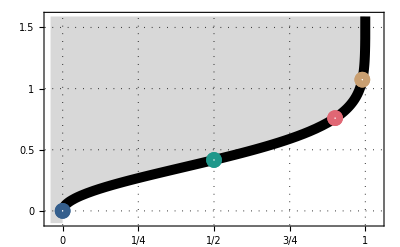

```mathematica
(* Plot the minimum required α to witness the state against z. *)
p3PPTCatInsetPlot=Quiet@Show[Plot[p3PPTCatIntersectionααz[z],{z,0,1},PlotTheme->"Detailed",PlotLegends->None,PlotRange->{{-0.04,1.04},{-0.09,1.59}},PlotStyle->{Black,Thickness[0.018]},Filling->Top,FillingStyle->Directive[Gray,Opacity[0.3]],FrameLabel->None,FrameTicks->{{{0,0.5,1,1.5},None},{{0,{0.25,"1/4"},{0.5,"1/2"},{0.75,"3/4"},1},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->11],GridLines->{{0,0.25,0.5,0.75,1},{0,0.5,1,1.5}},GridLinesStyle->Directive[Black,Thickness[0.002],Dotted]],Graphics[{Gray,Opacity[0.3],Rectangle[{-0.04,-0.1},{0,1.59}]}],ListPlot[{{{0,0}},{{0.5,p3PPTCatIntersectionααz[0.5]}},{{0.9,p3PPTCatIntersectionααz[0.9]}},{{0.99,p3PPTCatIntersectionααz[0.99]}}},PlotMarkers->{{NicePlotmarkers[9,0.28,White,PlotColors[[1]],1]},{NicePlotmarkers[9,0.28,White,PlotColors[[2]],1]},{NicePlotmarkers[9,0.28,White,PlotColors[[4]],1]},{NicePlotmarkers[9,0.28,White,PlotColors[[5]],1]}}],ImageSize->{Automatic,85}]
```

#### Plot

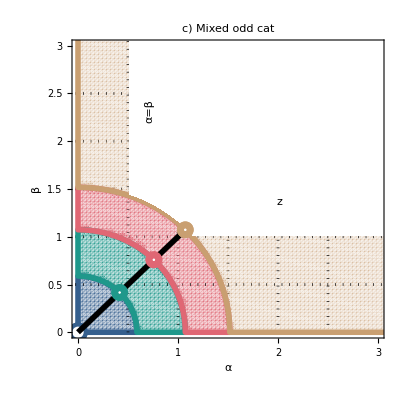

```mathematica
(* Plot the optimal p3-PPT criterion for the mixed Schrödinger cat state. *)
p3PPTCatPlot=Quiet[Show[RegionPlot[1>0,{α,0,4},{β,0,4},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->Opacity[0],BoundaryStyle->Opacity[0],PlotRange->{{0,3},{0,3}},PlotLegends->None,FrameLabel->{Style["α",Black,FontSize->15],Style["β",Black,FontSize->15]},FrameTicks->{{{0,0.5,1,1.5,2,2.5,3},None},{{0,0.5,1,1.5,2,2.5,3},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0.5,1,1.5,2,2.5},{0.5,1,1.5,2,2.5}},GridLinesStyle->Directive[Black,Thickness[0.005],Dotted],PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["c) ",Black,FontSize->16,Bold],Style["Mixed odd cat",Black,FontSize->15]}],Alignment->Center,ImageSize->170],Epilog->Inset[p3PPTCatInsetPlot,{1.85,2.2}]],Graphics[{White,Dashing[None],Rectangle[{0.51,1.45},{3,3}],Rectangle[{0.51,1.45},{3,3}],Opacity[0,PlotColors[[5]]],Rectangle[{0.51,1.45},{3,3}],Opacity[1],Black,FontSize->12,Text["z",{1.96,1.33}],Text["α",{0.6,2.3},Automatic,{0,1}]}],
RegionPlot[p3PPTCat[α,β,0]<0&&p3PPTCat[α,β,0.5]>0,{α,0,4},{β,0,4},PlotStyle->{PlotColors[[1]],Opacity[0.3]},BoundaryStyle->Directive[Thickness[0.01],PlotColors[[1]]],PlotPoints->InternalPlotPoints],
RegionPlot[p3PPTCat[α,β,0.5]<0&&p3PPTCat[α,β,0.9]>0,{α,0,4},{β,0,4},PlotStyle->{PlotColors[[2]],Opacity[0.3]},BoundaryStyle->Directive[Thickness[0.01],PlotColors[[2]]],PlotPoints->InternalPlotPoints],RegionPlot[p3PPTCat[α,β,0.9]<0&&p3PPTCat[α,β,0.99]>0,{α,0,4},{β,0,4},PlotStyle->{PlotColors[[4]],Opacity[0.3]},BoundaryStyle->Directive[Thickness[0.01],PlotColors[[4]]],PlotPoints->InternalPlotPoints],RegionPlot[p3PPTCat[α,β,0.99]<0,{α,0,4},{β,0,4},PlotStyle->{PlotColors[[5]],Opacity[0.15]},BoundaryStyle->Directive[Thickness[0.01],PlotColors[[5]]],PlotPoints->InternalPlotPoints],Plot[α,{α,0,1.1},PlotStyle->{{Black,Thickness[0.01]}}],RegionPlot[p3PPTCat[α,β,0.991]<0&&α≥0.51&&β≥1.01,{α,0,4},{β,0,4},PlotStyle->{White},BoundaryStyle->None,PlotPoints->InternalPlotPoints],ListPlot[{{{p3PPTCatIntersectionααz[0],p3PPTCatIntersectionααz[0]}},{{p3PPTCatIntersectionααz[0.5],p3PPTCatIntersectionααz[0.5]}},{{p3PPTCatIntersectionααz[0.9],p3PPTCatIntersectionααz[0.9]}},{{p3PPTCatIntersectionααz[0.99],p3PPTCatIntersectionααz[0.99]}}},PlotMarkers->{{NicePlotmarkers[16,0.15,White,PlotColors[[1]],1]},{NicePlotmarkers[10,0.28,White,PlotColors[[2]],1]},{NicePlotmarkers[10,0.28,White,PlotColors[[4]],1]},{NicePlotmarkers[10,0.28,White,PlotColors[[5]],1]}}],Graphics[{Black,FontSize->12,Text["z",{2.01,1.36}],Text["α=β",{0.71,2.315},Automatic,{0,1}]}],
ImageSize->{Automatic,250}]]
```

### High Harmonic Generation (HHG)

#### p_n-moments & criteria

```mathematica
(* Set up helper functions. *)
ν[δα_,n_,k_]:=Exp[-2*δα^2*(n-(2k+1))/(n^2+2n-3)];
γi[δα_]:=Exp[-(1/2)*δα^2]
γj[δα_,n_]:=Exp[-(1/2)*δα^2*(4/(n^2+2n-3))];
HHGNormalization[δα_,n_,k_]:=1-ν[δα,n,k]*(γi[δα]^2)*(γj[δα,n]^2);
```

```mathematica
(* Set up PT moments. *)

(* Implicit first, then simplify. *)
p2HHGImplicit[CNormalization_,ν_,γi_,γj_]:=(1/CNormalization^2)(1-4ν γi^2γj^2+2ν γi^4γj^4+2ν^2γi^2γj^2-ν^2γi^4γj^4);
p3HHGImplicit[CNormalization_,ν_,γi_,γj_]:=(1/CNormalization^3)(1-6ν γi^2γj^2+3ν γi^4γj^4+6ν^2γi^4γj^4+3ν^2γi^2γj^4+3ν^2γi^4γj^2-6ν^2γi^6γj^4-6ν^2γi^4γj^6+3ν^2γi^6γj^6-6ν^3γi^4γj^4+3ν^3γi^4γj^6+3ν^3γi^6γj^4-ν^3γi^6γj^6);
```

```mathematica
(* Final definitions. *)
p2HHG[δα_,n_,k_]=p2HHGImplicit[HHGNormalization[δα,n,k],ν[δα,n,k],γi[δα],γj[δα,n]]//Simplify;
p3HHG[δα_,n_,k_]=p3HHGImplicit[HHGNormalization[δα,n,k],ν[δα,n,k],γi[δα],γj[δα,n]]//Simplify;
```

```mathematica
(* Set up linear criterion. *)
p3PPTHHG[δα_,n_,k_]=p3HHG[δα,n,k]-(3/2)*p2HHG[δα,n,k]+(1/2)//Simplify;
```

#### Plot

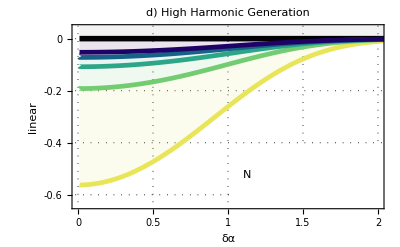

```mathematica
(* Plot the value of the linear witness against δα for various n. *)
p3PPTHHGPlot=Legended[Show[Plot[0,{δα,0.01,3},PlotRange->{{0,2},{-0.64,0.04}},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->{{Thickness[0.01],Black}},Filling->{1->{0.1,Directive[Gray,Opacity[0.1]]}},FrameLabel->{Style["δα",Black,FontSize->15],Style["linear",Black,FontSize->15]},FrameTicks->{{{-0.6,-0.4,-0.2,0},None},{{0,0.5,1,1.5,2},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,0.5,1,1.5,2},{-0.6,-0.4,-0.2,0}},GridLinesStyle->Directive[Black,Thickness[0.002],Dotted],PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["d) ",Black,FontSize->16,Bold],Style["High Harmonic Generation",Black,FontSize->15]}],Alignment->Center,ImageSize->{210,30}]],Plot[{p3PPTHHG[δα,3,1],p3PPTHHG[δα,5,1],p3PPTHHG[δα,7,1],p3PPTHHG[δα,9,1],p3PPTHHG[δα,11,1]},{δα,0.01,3},PlotRange->{{0,2},{-0.6,0.1}},PlotStyle->{{Thickness[0.0085],ContinuousColors[1]},{Thickness[0.0085],ContinuousColors[2]},{Thickness[0.0085],ContinuousColors[3]},{Thickness[0.0085],ContinuousColors[4]},{Thickness[0.0085],ContinuousColors[5]}},Filling->{1->{{2},Directive[ContinuousColors[1],Opacity[0.1]]},2->{{3},Directive[ContinuousColors[2],Opacity[0.1]]},3->{{4},Directive[ContinuousColors[3],Opacity[0.1]]},4->{{5},Directive[ContinuousColors[4],Opacity[0.1]]},5->{0,Directive[ContinuousColors[5],Opacity[0.1]]}}],Graphics[{White,Rectangle[{1.01,-0.7},{2.1,-0.41}],Black,FontSize->15,Text["N",{1.13,-0.525}]}],AspectRatio->1/GoldenRatio,ImageSize->{Automatic,236.5}],Placed[BarLegend[{ContinuousColors,{1,5}},LabelStyle->{Black,FontSize->13},LegendLayout->"Row",LegendMarkerSize->110,Ticks->{1,2,3,4,5}],{0.755,0.165}]]
```

Genuine non-Gaussian states

### NOON states

#### p_n-moments & criteria

```mathematica
(* Set up the k-th. moment in terms of the phase α. *)
pnNOON[α_,k_]:=If[OddQ[k]==True,Abs[α]^(2*k)+(1-Abs[α]^2)^k,(Abs[α]^k+(1-Abs[α]^2)^(k/2))^2]//Simplify;
```

```mathematica
(* Set up the general criterion. *)
pnPPTNOON[α_,k_]:=Table[pnNOON[α,i+j+1],{i,0,(k-1)/2,1},{j,0,(k-1)/2,1}]//Simplify;
```

```mathematica
(* Set up the special case n=3. *)
p3PPTNOON[α_]=Det[Table[pnNOON[α,i+j+1],{i,0,1,1},{j,0,1,1}]]//Simplify;
```

#### Plot

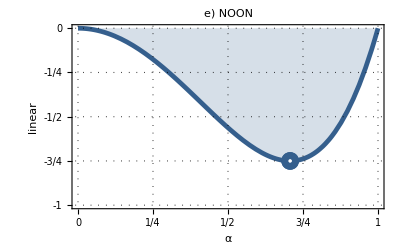

```mathematica
(* We plot the LHS-RHS of the p3-PPT criterion. *)
p3PPTNOONPlot=Show[Plot[{p3PPTNOON[α]},{α,0,1},PlotRange->{{0,1},{-1,0}},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->{{PlotColors[[1]],Thickness[0.0085]}},PlotLegends->None,FrameLabel->{Style["α",Black,FontSize->15],Style["linear",Black,FontSize->15]},FrameTicks->{{{-1,{-0.75,"-3/4"},{-0.5,"-1/2"},{-0.25,"-1/4"},0,{0.25,"1/4"}},None},{{0,{0.25,"1/4"},{0.5,"1/2"},{0.75,"3/4"},1},None}},FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[Black,FontSize->15],GridLines->{{0,0.25,0.5,0.75,1},{-1,-0.75,-0.5,-0.25,0,0.25}},GridLinesStyle->Directive[Black,Thickness[0.002],Dotted],Filling->0,PlotLabel->Pane[Apply[StringJoin,ToString[#,StandardForm]&/@{Style["e) ",Black,FontSize->16,Bold],Style["NOON",Black,FontSize->15]}],Alignment->Center,ImageSize->70]],ListPlot[{{1/Sqrt[2],-0.75}},PlotMarkers->NicePlotmarkers[11,0.28,White,PlotColors[[1]],1]],Graphics[{White,Rectangle[{0,-5/4},{0.49,-1.01}],FontSize->15,PlotColors[[1]],Text["PPT3",{0.125,-1.125}],PlotColors[[2]],Text["PPT5",{0.375,-1.125}]}],ImageSize->{Automatic,230}]
```

Combined figure

```mathematica
(* Assemble upper and lower rows of the final figure. *)
MainFigureUpperRow=Grid[{{p3GaussianPlot,p3GaussianPlot2,p3PPTCatPlot}},Alignment->{Left,Bottom},Spacings->1];
MainFigureLowerRow=Grid[{{p3PPTHHGPlot,p3PPTNOONPlot}},Alignment->{Left,Bottom},Spacings->{3.8}];
```

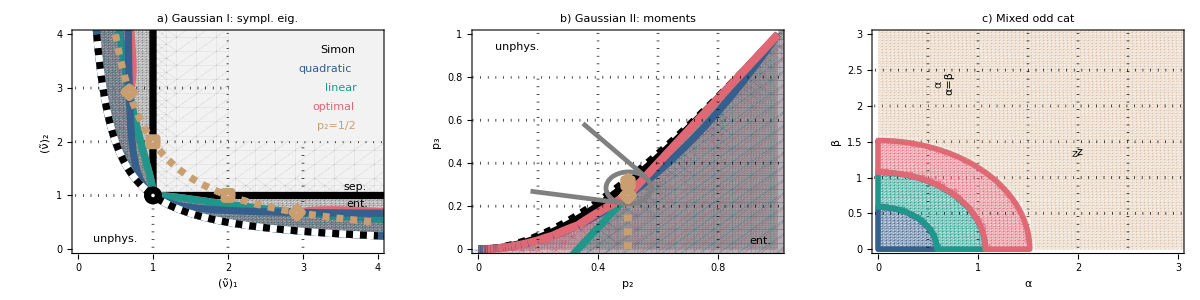
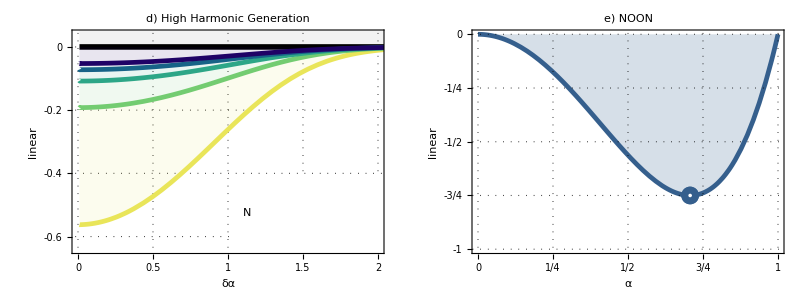

```mathematica
(* Combine all five figures into a single one. *)
MainFigure=Grid[{{MainFigureUpperRow},{MainFigureLowerRow}},Alignment->Left,Spacings->{0,0.1}]
```